## Images

```mathematica
cdata=ChemicalData[];
```

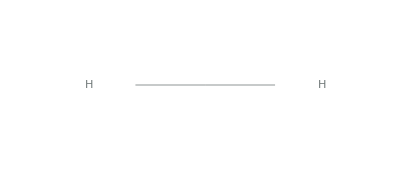

```mathematica
ChemicalData[cdata[[1]]]
```

```mathematica
r=Rasterize[ChemicalData[cdata[[1]]]]
```

-Graphics-

```mathematica
i=Image[ChemicalData[cdata[[1]]]]
```

-Graphics-

```mathematica
ImageData[i]//Dimensions
```

{21,42,3}

```mathematica
s=ChemicalData[cdata[[1]],"SMILES"]
```

[HH]

```mathematica
Information[i]
```

Image

### train test

```mathematica
NetTrain[{1->s,1->s}]
```

NetTrain[{1→[HH],1→[HH]}]